```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
A=Import["matrices/A.dat"][[2;;]];
```

```mathematica
MatrixPlot[A,MaxPlotPoints->∞]
```

-Graphics-

```mathematica
{λ,ψ}=Eigensystem@A;
```

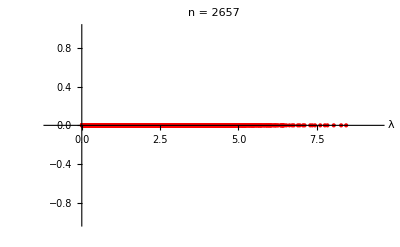

```mathematica
ListPlot[{#,0}&/@λ,
PlotLabel->"n = "<>ToString@Length@A,
Axes-> {True,False},
AxesLabel->{"λ"},
PlotRange->{{Last@λ-1,First@λ+1},Automatic}, 
PlotStyle->{PointSize[Medium],Red},
ImageSize->Full]
```

```mathematica
Last@λ
```

0.00209639